## How fast can a core grow by gravitational focusing of planetesimals/pebbles?

```mathematica
Clear["Global`*"]
AU = 1.496*^13;
μ=3.85*^-24;
k=1.381*^-16;
G=6.67259*^-8;
Msun = 1.9891*^33;
Σ = 500*Σ500*AU*a^-1;
Σp = Σ/100;
ρs=2;
σ=10^-15;
Mstar=Msun;
Mearth = 5.976*^27;

vth = √((8 k T)/(π μ));
T = 200*T200*AU^(3/7)*a^(-3/7);
tsEps=r/vth*ρs/ρg;
Ω=√((G Mstar)/a^3);
cs = √((k T)/μ);
H = cs/Ω;
ρg = Σ/(2 H);
λ=μ/(ρg σ);
vth = √((8 k T)/(π μ));
vk = a Ω;
η=cs^2/(2 vk^2);
vpgLam=η vk (√(1 + 4 St^2))/(1+St^2);
vpgTurb=√α cs √(St/(1+St));
vrel = √(vpgLam^2+vpgTurb^2);
Ren=(2 s vrel)/(0.5 vth λ);
Cd = 24/Ren(1+0.27*Ren)^0.43+0.47*(1-Exp[-0.04*Ren^0.38]);
FdStoRam=1/2*Cd*π*s^2*ρg*vrel^2;
m=4/3 π s^3 ρs;
rh=a*(Mp/(3 Msun))^(1/3);
vh=rh*Ω;
rp=((3 Mp)/(4 π ρs))^(1/3);
```

```mathematica
tgrowpla=Mp/(6π rh rp Σp Ω)/3.154*^7/.a->A*AU/.Mp->M*Mearth
Solve[tgrowpla==τyears*2.5*^6,M]
```

(75502.2 M^(1/3))/(√(1/A^3) Σ500)

{{M→36302.8 (1/A^3)^(3/2) Σ500^3 τyears^3}}

```mathematica
36302.840332959226 (1/A^3)^(3/2) Σ500^3 τyears^3/.A->30
```

0.00818267 Σ500^3 τyears^3

## Try GF of Pebbles

```mathematica
v0= η vk ;
vesc = √((2 G Mp)/rp);
bGF =rp √((vesc/v0)^2);
bGFvh=rp(vesc/vh);
(*MdotGFpeb=2*Σp**)
```

```mathematica
FullSimplify[bGF/(2η vk/Ω)/.a->A*AU/.Mp->M*Mearth,Assumptions->{A>0,M>0}]
FullSimplify[bGFvh/(2η vk/Ω)/.a->A*AU/.Mp->M*Mearth,Assumptions->{A>0,M>0}]
FullSimplify[vesc/v0/.a->A*AU/.Mp->M*Mearth,Assumptions->A>0]
```

(57.9453 M^(2/3) √(1/T200^2))/(A^(23/14) T200)

(2.34164 M^(1/3))/(A^(15/14) T200)

(784.505 M^(1/3))/(A^(1/14) T200)

```mathematica
α=α3*10^-3;
Ht=√(α/St)H;
bGFt=rp √((vesc/(√α cs))^2)
FullSimplify[bGFt/Ht/.a->A*AU/.Mp->M*Mearth,Assumptions->{A>0,M>0,T200>0,α3>0}]
(*bGFt/.Mp->M*Mearth/.a->A*AU*)
```

2.76193×10^-7 Mp^(1/3) √((a^(3/7) vesc^2)/(T200 α3))

(0.0000247978 M^(1/3) √(vesc^2))/(A^(15/14) √(1/St) T200 α3)

```mathematica
1/3 1000^2/(α cs^2)/.a->A*AU
```

(0.0000464639 A^(3/7))/(T200 α)

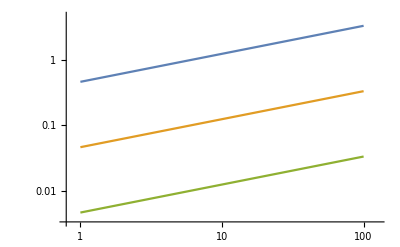

```mathematica
LogLogPlot[Evaluate[(0.00004646391503741251 A^(3/7))/(T200 α)/.T200->1/.α->{10^-4,10^-3,10^-2}],{A,1,100}]
```

### Plot expressions for 2D-3D regimes

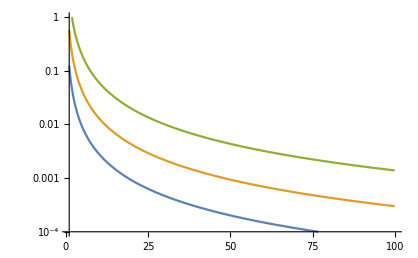

```mathematica
LogPlot[Evaluate[(57.94525590775855 M^(2/3) √(1/T200^2))/(A^(23/14) T200)/.T200->1/.M->{10^-4,10^-3,10^-2}],{A,1,100},PlotRange->{{1,100},
{10^-4,10^0}}]
```

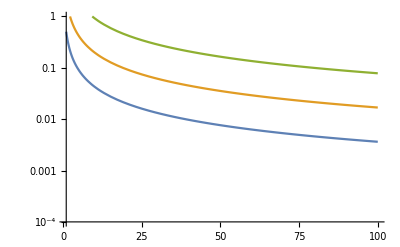

```mathematica
LogPlot[Evaluate[(23.427792571310153 M^(2/3))/(A^(15/14) √(1/St) T200 α3)/.α3->10^-1/.St->1/.T200->1/.M->{10^-4,10^-3,10^-2}],{A,1,100},PlotRange->{{1,100},
{10^-4,10^0}}]
```

## So growth being 3D isn’t a bad assumption. Now make sure that expressions agree when v_H=vgas.

```mathematica
Mp/.Solve[bGF==bGFvh,Mp]⟦3⟧
```

10.2405 a^(12/7) T200^3

```mathematica
Solve[vh/v0==1,Mp]
```

{{Mp→10.2405 a^(12/7) T200^3}}

## Growth Timescale for GF of Pebbles

## With Turbulence

```mathematica
ρpt=Σp/(2 Ht);
v∞t=√α cs;
σacct = 4*bGFt^2
MdotGFt=ρpt*σacct*v∞t
(*FullSimplify[MdotGFt/.T200->*)
tgrowGFt=FullSimplify[Mp/MdotGFt/3.154*^7/.Mp->M*Mearth/.a->A*AU,Assumptions->{A>0,α3>0}]
```

(8.2702×10^-20 a^(3/7) Mp^(4/3))/(T200 α3)

(3.56339×10^7 √(1/a^3) Mp^(4/3) Σ500)/(a^(4/7) T200 √α3 √(α3/St))

(958.079 A^(29/14) √(1/St) T200 α3)/(M^(1/3) Σ500)

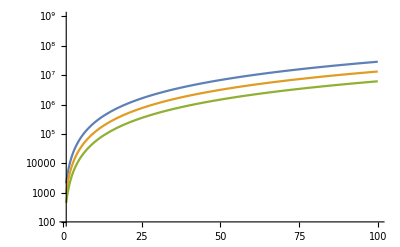

```mathematica
LogPlot[Evaluate[(958.0790712390278 A^(29/14) √(1/St) T200 α3)/(M^(1/3) Σ500)/.α3->10^-1/.St->1/.T200->1/.Σ500->1/.M->{10^-4,10^-3,10^-2}],{A,1,100},PlotRange->{{1,100},
{100,10^9}}]
```

```mathematica
Clear["Global`*"]
AU = 1.496*^13;
μ=3.85*^-24;
k=1.381*^-16;
G=6.67259*^-8;
Msun = 1.9891*^33;
Σ = 500*Σ500*AU*a^-1;
Σp = Σ/100;
ρs=2;
σ=10^-15;
Mstar=Msun;
Mearth = 5.976*^27;

vth = √((8 k T)/(π μ));
(*T = 200*T200*AU^(3/7)*a^(-3/7);*)
Tvisc = 200*T200*α3^(-1/5)*(a/AU)^(-9/10)
tsEps=r/vth*ρs/ρg;
Ω=√((G Mstar)/a^3);
cs = √((k Tvisc)/μ);
H = cs/Ω;
ρg = Σ/(2 H);
λ=μ/(ρg σ);
vth = √((8 k Tvisc)/(π μ));
vk = a Ω;
η=cs^2/(2 vk^2);
vpgLam=η vk (√(1 + 4 St^2))/(1+St^2);
vpgTurb=√α cs √(St/(1+St));
vrel = √(vpgLam^2+vpgTurb^2);
Ren=(2 s vrel)/(0.5 vth λ);
Cd = 24/Ren(1+0.27*Ren)^0.43+0.47*(1-Exp[-0.04*Ren^0.38]);
FdStoRam=1/2*Cd*π*s^2*ρg*vrel^2;
m=4/3 π s^3 ρs;
rh=a*(Mp/(3 Msun))^(1/3);
vh=rh*Ω;
rp=((3 Mp)/(4 π ρs))^(1/3);
StEps=ρs/ρg s/vth Ω;
rws=rh √(3 St vh/vgas);
v0= η vk ;
Solve[rp==rws/.St->12 vh^3/vgas^3,Mp]
```

(1.44035×10^14 T200)/(a^(9/10) α3^(1/5))

{{Mp→0.},{Mp→-7.08686×10^9 vgas^3},{Mp→(0.-7.08686×10^9 ⅈ) vgas^3},{Mp→(0.+7.08686×10^9 ⅈ) vgas^3},{Mp→7.08686×10^9 vgas^3}}

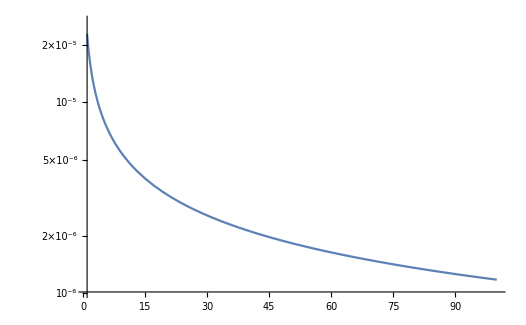

```mathematica
LogPlot[(7.086863103716389*^9 vgas^3)/Mearth/.vgas->√(1*^-1)cs/.a->A*AU/.T200->1,{A,1,100}]
```

```mathematica
Clear["Global`*"]
rh=a*(Mp/(3 Mstar))^(1/3);
vh=rh*Ω;
Ω=√((G Mstar)/a^3);
rws=rh √(3 St vh/vgas);
rp=((3 Mp)/(4 π ρs))^(1/3);
FullSimplify[Solve[rp==rws/.St->12 vh^3/vgas^3,Mp]]
```

{{Mp→0},{Mp→-(√(3/(2 π)) vgas^3)/(4 G^(3/2) √ρs)},{Mp→-(ⅈ √(3/(2 π)) vgas^3)/(4 G^(3/2) √ρs)},{Mp→(ⅈ √(3/(2 π)) vgas^3)/(4 G^(3/2) √ρs)},{Mp→(√(3/(2 π)) vgas^3)/(4 G^(3/2) √ρs)}}

```mathematica
Clear["Global`*"]
Integrate[1/(2 v0 τs0 (r/r0)^α),{r,redge,rin}]
```

ConditionalExpression[((redge (redge/r0)^-α)/(-1+α)-(rin (rin/r0)^-α)/(-1+α))/(2 v0 τs0),((Im[redge] Re[r0]+Im[r0] (-Re[redge]+Re[rin])≤Im[rin] Re[r0]&&(Im[redge] Re[r0]≥Im[r0] Re[redge]||Im[rin] Re[redge]≥Im[redge] Re[rin]||Im[rin] Re[r0]≤Im[r0] Re[rin]))||(Im[redge] Re[r0]+Im[r0] (-Re[redge]+Re[rin])≥Im[rin] Re[r0]&&(Im[rin] Re[r0]≥Im[r0] Re[rin]||Im[redge] Re[r0]≤Im[r0] Re[redge]||Im[rin] Re[redge]≤Im[redge] Re[rin])))&&(redge/(redge-rin)∉Reals||Re[redge/(redge-rin)]>1||(redge≠0&&redge^2≠redge rin&&Re[redge/(-redge+rin)]≥0))]

## Limiting Mass

```mathematica
Clear[α]
vgas=√α cs
FullSimplify[Mp/Mearth/.Solve[3 (vh^3 vgas)/cs^4==St,Mp]/.a->A*AU/.α->10^-3*α3/.St->10^-2*St2,Assumptions->A>0]
FullSimplify[Mp/Mearth/.Solve[9 vh^6/cs^6==St,Mp]/.a->A*AU/.α->10^-3*α3/.St->10^-2*St2,Assumptions->A>0]
```

7.18788×10^10 √α √(T200/(a^(9/10) α3^(1/5)))

{(2.42026 A^(3/20) St2 (T200/α3^(1/5))^(3/2))/(√α3)}

{-(0.765352 A^(3/20) √St2 T200^(3/2))/α3^(3/10),(0.765352 A^(3/20) √St2 T200^(3/2))/α3^(3/10)}

## St_Frag

```mathematica
StFrag=1/3 uf^2/(α cs^2)/.α->α3*10^-3/.uf->u1000*1000/.a->A*AU
```

(0.0464639 A^(9/10) u1000^2)/(T200 α3^(4/5))

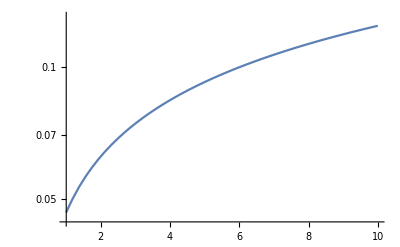

```mathematica
LogPlot[StFrag/.T200->1/.α3->1/.u1000->1,{A,1,10}]
```

```mathematica
FullSimplify[(0.7653520494508409 A^(3/20) √St2 T200^(3/2))/α3^(3/10)/.St2->((0.0464639150374125 A^(9/10) u1000^2)/(T200 α3^(4/5))/10^-2),Assumptions->{A>0,α3>0,T200>0,u1000>0}]
FullSimplify[(2.4202556881424773 A^(3/20) St2 (T200/α3^(1/5))^(3/2))/(√α3)/.St2->((0.0464639150374125 A^(9/10) u1000^2)/(T200 α3^(4/5))/10^-2),Assumptions->{A>0,α3>0,T200>0,u1000>0}]
```

(1.64975 A^(3/5) T200 u1000)/α3^(7/10)

(11.2455 A^(21/20) √T200 u1000^2)/α3^(8/5)